```mathematica
Clear["Global`*"];
SetDirectory@NotebookDirectory[];
```

```mathematica
CloudGet["https://www.wolframcloud.com/objects/8549bab6-7b14-4b2a-b77a-8944882d6562"]
```

# How to Fix the House of Representatives

Okay, we have everything we need to start a computational experiment on how the House of Representatives--and, by extension, the Electoral College--could be adjusted for better representation without the need for a Constitutional amendment. In the process of toying with the size of the House and the algorithm for how the seats are allotted, we’ll be recalculating the results of the 2016 election if our adjustments were to have taken place.

The Constitution stipulates that the number of representatives per state should be reapportioned after each decennial census based on state populations. It does not specify the total number of representatives or the exact method of allotment, other than specifying that each state should have at least one representative.

Since the 1940 Census, the United States has used the Huntington-Hill algorithm, known as the "method of equal proportions," to divvy up the 435 House seats. This begins by allotting one electoral vote to each state, leaving 385 left. The 50 states are then allotted these remaining seats one-by-one according to which one has the highest priority as determined by a simple equation: its population divided by the square root of its current seats times one extra seat (the Geometric Mean):

P/(√(n (1+n)))

We’re going to start by using this algorithm and adjusting the size and default starting and ending points. Then we’ll toy around with other algorithms. Each one we consider will take just two arguments: The population of the state and its current number of seats during the iterative process of assigning them, like so:

PriorityHuntingtonHill[stateAbbr_, stateReps_] := 
	1.0 * statesByAbbreviation[stateAbbr][“population_decennial”][“2010”] / 	Sqrt[stateReps * (stateReps + 1)]

The way the allocation works is to keep calculating priorities until you run out of seats. We may want to fuss with this method as well.

AllocateOne[reps_, priorities_, priorityFunc_:PriorityHuntingtonHill] := (
	topPriority = First[Keys[Reverse[Sort[priorities]]]];
	updatedPriorities = priorities;
	updatedReps = reps;
	updatedReps[topPriority] += 1;
	updatedPriorities[topPriority] = priorityFunc[topPriority, updatedReps[topPriority]];
	{ updatedReps, updatedPriorities }
);

CalculateAllocations[totalBase_:435, min_:1, bonus_:0, priorityFunc_:PriorityHuntingtonHill]:= (
	total = totalBase + 50 * -bonus; (* we need to add the post-facto bonus to the total so that it doesn’t count against it *)
	stateReps = AssociationThread[stateAbbrs50, ConstantArray[min, 50]];
	statePriorities = AssociationThread[stateAbbrs50, priorityFunc[#, 1]& /@ stateAbbrs50];
	While[Total@stateReps < total, { stateReps, statePriorities } = AllocateOne[stateReps, statePriorities, priorityFunc]];
	stateReps = stateReps + bonus;
	KeySort@stateReps
);

## Let’s see if there’s an ideal size of the House

One of the beauties of the Wolfram language is that it lends itself to running computational experiments. Let’s try a bunch of different House sizes, up to twice the current size, and see if there’s an ideal number of representatives for the lowest variance in the representative-per-person ratios from state-to-state.

```mathematica
GetVariance[houseSize_] := (
	allocation = CalculateAllocations[houseSize, 1, 0, PriorityHuntingtonHill];
	ratio = PeoplePerRepresentative[allocation];
	sd = StandardDeviation[ratio] * 1.0;
	cov = sd / Mean@ratio
)
```

This will take just a second since we’re running about 700 simulations, all of which require taking a lot of square roots.

```mathematica
houseSizes = Range[150,870];
variances = GetVariance /@ houseSizes;
```

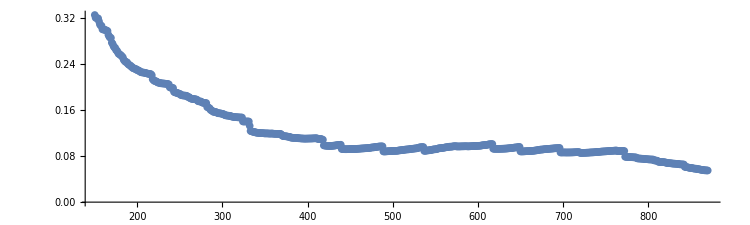

```mathematica
ListPlot[Transpose[{houseSizes, variances}], ImageSize->750, AspectRatio->0.3, PlotRange->Automatic, PlotRange->All]
```

This is a curious result. We’d certainly expect the variance decline as the House grows larger, but there are certain breaking points where one extra seat significantly reduces the disparity. This won’t fix the problem by itself, but let’s identify those points where there is at least a modest drop.

```mathematica
indices = Select[Most[Range[Length@variances]], variances[[#]] / variances[[# + 1 ]] > 1.05&] + 1;
values = variances[[#]]& /@ indices;
idealSizes = houseSizes[[#]]& /@ indices
```

{332,333,419,440,489,537,618,650,697,773,843}

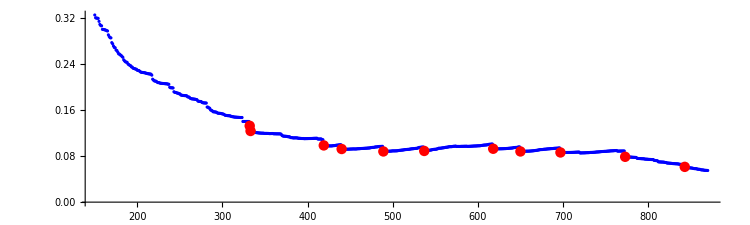

```mathematica
ListPlot[{Transpose[{houseSizes, variances}], Transpose[{idealSizes, values}]},
	ImageSize -> 750, AspectRatio -> 0.3, PlotRange->Full, PlotStyle->{{Blue, PointSize[0.003]},{Red, PointSize[0.01]}}
]
```

Now, out of curiosity, let’s see what the per-representatives ratios looks like at a few of these points compared to the current House.

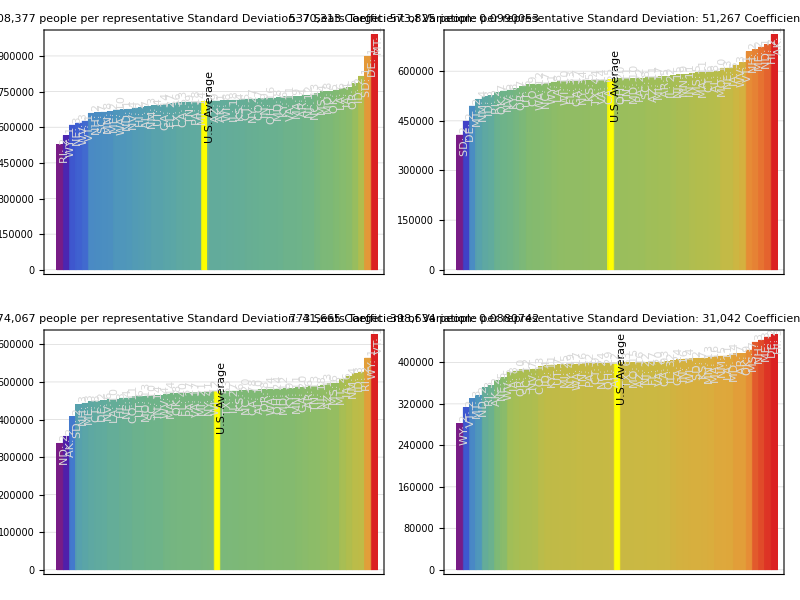

```mathematica
Grid[{
	{
		Magnify[VisualizeRepresentation[houseOfRepresentatives], 0.5],
		Magnify[VisualizeRepresentation[CalculateAllocations[537]], 0.5]
	},
	{
		Magnify[VisualizeRepresentation[CalculateAllocations[650]], 0.5],
		Magnify[VisualizeRepresentation[CalculateAllocations[773]], 0.5]
	}
}]
```

```mathematica
statePopulations = AssociationThread[stateAbbrs50, statesByAbbreviation[#]["population_decennial"]["2010"]& /@ stateAbbrs50];
totalPopulation = Total@statePopulations;
```

```mathematica
GetDisenfranchised[houseSize_] := (
	targetPeoplePerRep = totalPopulation / houseSize;
	allocation = CalculateAllocations[houseSize, 1, 0, PriorityHuntingtonHill];
	peoplePerRep = PeoplePerRepresentative[allocation];
	ratios = 1.0 - peoplePerRep / targetPeoplePerRep;
	disenfranchised = AssociationThread[stateAbbrs50, (ratios[#] * statePopulations[#])& /@ stateAbbrs50]
)
```

```mathematica
disenfranchisement = GetDisenfranchised /@ houseSizes;
```

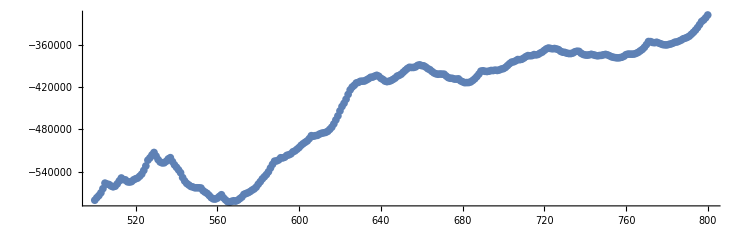

```mathematica
ListPlot[Transpose[{houseSizes, Total /@ disenfranchisement}], ImageSize->750, AspectRatio->0.3]
```

## New algorithm

```mathematica
PriorityHuntingtonHill[stateAbbr_, stateReps_] := 
	1.0 * statesByAbbreviation[stateAbbr]["population_decennial"]["2010"] / Sqrt[stateReps * (stateReps + 1)]
```

```mathematica
interactive = Manipulate[(
		allocation = CalculateAllocations[total, min, bonus, PriorityHuntingtonHill];
		grid = HorizontalGrid[allocation, 26];
		electionResultsPresident = RerunElectionPresident[allocation, 3];	
		resultBox = ResultBox[electionResultsPresident["result"]];
		perRep = VisualizeRepresentation[allocation, "New Allocation"];
		electionResultsCongress = RerunElectionCongress[allocation];
		houseChart = ChartElectionCongress[electionResultsCongress];
		prezChart = ChartPresidentialElection[electionResultsPresident];

		Column[{
			resultBox,
			houseChart,
			Style["Comparison of Allocation", FontSize->14, Bold, TextAlignment->Center],
			grid,
			perRep
		}, Alignment->Center]
	),
	Grid[{
		{
			Control[{{ total, 435, "Total Reps:"}, 50, 2000, 1, Appearance -> "Open" }],
			Control[{{ min, 1, "Start With:"}, 0, 40, 1, Appearance -> "Open" }],
			Control[{{ bonus, 0, "Add at End:"}, -20, 20, 1, Appearance -> "Open" }]
		}
	}, Alignment->Center],
	LabelStyle->{ FontSize -> 13 }
]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression -30404965+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression -29910257+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression -29878681+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Max::nord: Invalid comparison with ComplexInfinity attempted.